# Load Files

```mathematica
SetDirectory[NotebookDirectory[]];
Get[FileNameJoin[{Directory[],"PentaBoxModules.m"}]];
Get[FileNameJoin[{Directory[],"DifferentialOperator.m"}]];
$P=2^31-1;
PureIntegrals=ReadList[FileNameJoin[{NotebookDirectory[],"files/PureIntegralBasis2.txt"}]];


LaportaBasis=ReadList[FileNameJoin[{Directory[],"masters"}]];
LaportaBasis=Cases[LaportaBasis,_TTH,Infinity];
```

# Generate Phase-Space Point

{d→633636893,mTsq→755795428,qsq→761598219,s12→1600327277,s15→1392605904,s23→668282060,s34→201572535,s45→1736032107}

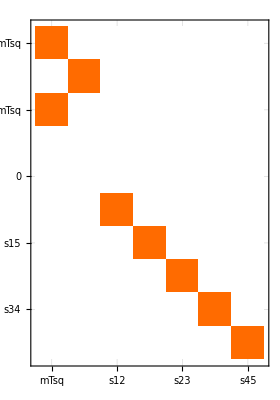

(1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
tPoint=GetRandomPT[0,$P]
DeleteOldKiraRun[]
WriteNumericsFile[tPoint]
PureIntegralN=Expand[PureIntegrals/.tPoint/.root[n_]:>PowerMod[n,1/2,$P],Modulus->$P];
diffOp=getDifferentialOperator[tPoint];
epsrepl={(ep->(4-d)/2)/.tPoint};
checkDifferentialOperator[tPoint,diffOp]
```

# Compute Basis Change Matrix

0

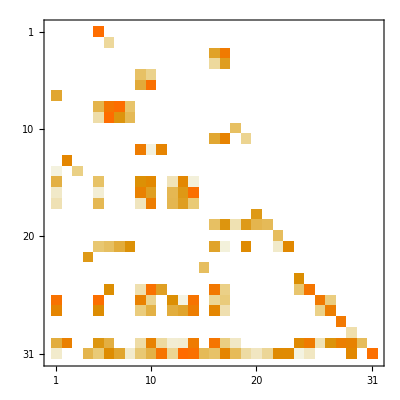

```mathematica
reductionRules=GetReductionTableFromFile[FileNameJoin[{NotebookDirectory[],"KIRA/results/TTH/numerics_2147483647_0.m"}]];
PureIntegralN2=Expand[PureIntegralN/.reductionRules,Modulus->$P];
Basis=Cases[PureIntegralN2,_TTH,Infinity]//DeleteDuplicates;
NullInts=Thread[Rule[Complement[Basis,LaportaBasis],0]]//EchoFunction[Length];
PureIntegralN2=PureIntegralN2/.NullInts;
BasisChangMat=Table[CoefficientArrays[Expand[PureIntegralN2/.epsrepl,Modulus->$P][[pos]],LaportaBasis],{pos,1,31}];
BasisChangMat=Normal[BasisChangMat[[All,2]]];
BasisChangMatInv=Inverse[BasisChangMat,Modulus->$P];
BasisChangMat//MatrixPlot
```

# Compute DE Matrix Pre IBP

```mathematica
loopMomentumScalarProductsT=Expand[loopMomentumScalarProducts/.tPoint,Modulus->$P];
mandelstamScalarProductsT=Expand[mandelstamScalarProducts/.tPoint,Modulus->$P];
Monitor[diffInts=Table[
Expand[Expand[(applyDifferentialOperator[Collect[Coefficient[diffOp,ds[invariantsnodUpperCase[[var]]]],del[___]],Expand[PureIntegrals[[intpos]]/.tPoint[[Delete[{1,2,3,4,5,6,7,8},var+1]]]/.epsrepl,Modulus->$P]]/.tPoint/.root'[x_]:>1/(2 root[x]))/.root[x_]:>PowerMod[x,1/2,$P],Modulus->$P]/.loopMomentumScalarProductsT/.mandelstamScalarProductsT,Modulus->$P],{var,1,Length[invariantsnodUpperCase]},{intpos,1,Length[PureIntegrals]}],ProgressIndicator[(var-1)*31+intpos,{1,31*7}]];
```

## Extra Step If Redu List does not exits yet

```mathematica
ToReduce=Cases[diffInts,_TTH,Infinity]//DeleteDuplicates//EchoFunction[Length];
Export[FileNameJoin[{NotebookDirectory[],"KIRA/ReduList.txt"}],ToReduce];
GenerateSectorsFromReductionList[FileNameJoin[{NotebookDirectory[],"KIRA/ReduList.txt"}]];
DeleteOldKiraRun[]
WriteNumericsFile[tPoint]
```

325

```mathematica
ToReduce2=Cases[PureIntegralN,_TTH,Infinity]//DeleteDuplicates//EchoFunction[Length];
Export[FileNameJoin[{NotebookDirectory[],"KIRA/UReduList.txt"}],ToReduce2];
GenerateSectorsFromReductionList[FileNameJoin[{NotebookDirectory[],"KIRA/UReduList.txt"}]];
DeleteOldKiraRun[]
WriteNumericsFile[tPoint]
```

32

```mathematica
WriteJobFile[{"UReduList","ReduList"}]
```

# Apply IBP Reduction

```mathematica
diffIntsIBREDUCED=Expand[diffInts/.reductionRules,Modulus->$P];
NonReduced=Cases[diffIntsIBREDUCED,_TTH,Infinity]//DeleteDuplicates//EchoFunction[Length];
NullInts2=Complement[NonReduced,LaportaBasis];
diffIntsIBREDUCED=diffIntsIBREDUCED/.Thread[Rule[NullInts2,0]];
```

34

# Compute DE Matrices

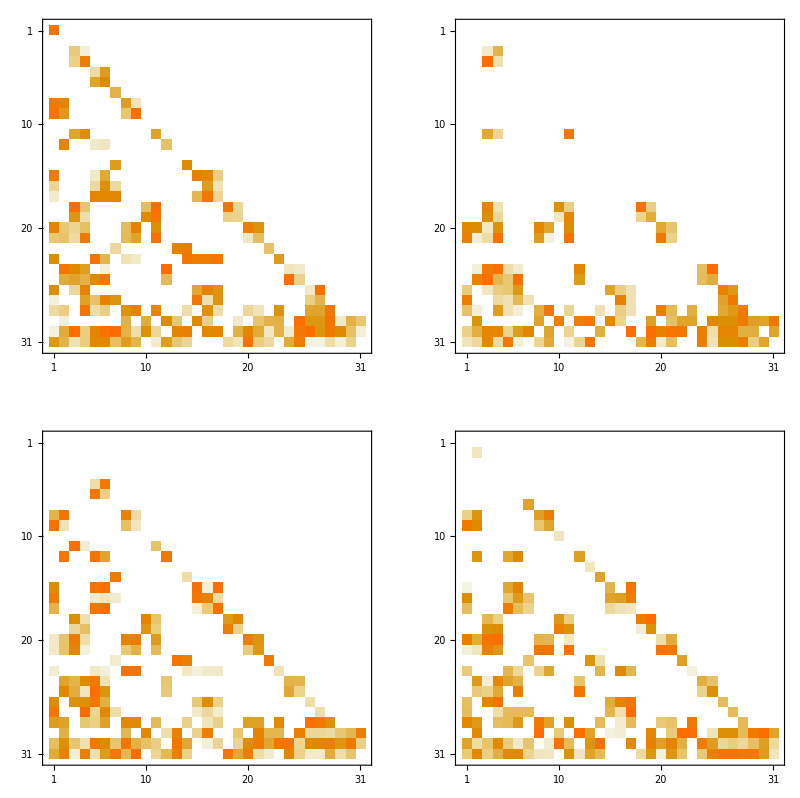

-Graphics-

```mathematica
dhxbMatrices=Table[Normal[CoefficientArrays[diffIntsIBREDUCED[[i,j]],LaportaBasis]/.{0}->{0,ConstantArray[0,31]}][[2]],{i,1,Length[invariants]-1},{j,1,Length[LaportaBasis]}];
Mplot1=MatrixPlot[Expand[dhxbMatrices[[1]].BasisChangMatInv,Modulus->$P]];
Mplot2=MatrixPlot[Expand[dhxbMatrices[[2]].BasisChangMatInv,Modulus->$P]];
Mplot3=MatrixPlot[Expand[dhxbMatrices[[3]].BasisChangMatInv,Modulus->$P]];
Mplot4=MatrixPlot[Expand[dhxbMatrices[[4]].BasisChangMatInv,Modulus->$P]];
Mplot5=MatrixPlot[Expand[dhxbMatrices[[5]].BasisChangMatInv,Modulus->$P]];
Mplot6=MatrixPlot[Expand[dhxbMatrices[[6]].BasisChangMatInv,Modulus->$P]];
Mplot7=MatrixPlot[Expand[dhxbMatrices[[7]].BasisChangMatInv,Modulus->$P]];
GraphicsGrid[{{Mplot1,Mplot4},{Mplot5,Mplot7}}]
GraphicsGrid[{{Mplot2,Mplot3},{Mplot6}}]
```